```mathematica
filenames={"Table_TwoHerbicides_Stochastic_control13_sexualReproduction1_seedbank1_cost1_300_cost2_300_kCost1_5_kCost2_5_kHerb1_5_kHerb2_5_fieldsize10000.txt"};
```

```mathematica
data=Table[Import[NotebookDirectory[]<>"../data/"<>filenames⟦i⟧,"CSV"],{i,1,Length[filenames],1}];
```

## Plant density/m^2

```mathematica
plottab=Table[gatherruns=GatherBy[data⟦j,2;;,{1,6,2}⟧,Last];
Show[ListLogPlot[Table[gatherruns⟦i⟧⟦All,2⟧,{i,1,1000,1}],Joined->True,PlotStyle->Directive[Lighter[RGBColor["#3C4C59"],0.5],Thickness[0.001]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003],16],FrameLabel->None],
ListLogPlot[gatherruns⟦1001⟧⟦All,2⟧,Joined->True,Mesh->True,PlotStyle->Directive[Full,RGBColor["#3C4C59"]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003],16],FrameLabel->None],PlotRange->{{0,30},{0,6}},Axes->None],{j,1,Length[data],1}];
```

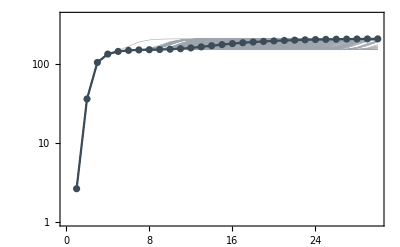

```mathematica
plottab⟦1⟧
```

## Plant numbers

```mathematica
{rwcol,rrcol,wwcol}={RGBColor["#F2A35E"],RGBColor["#BF766F"],RGBColor["#7C92A6"]}
```

{RGBColor[0.9490196078431372, 0.6392156862745098, 0.3686274509803922],RGBColor[0.7490196078431373, 0.4627450980392157, 0.43529411764705883],RGBColor[0.48627450980392156, 0.5725490196078431, 0.6509803921568628]}

```mathematica
datasummed = {data⟦1,2;;,1⟧, data⟦1,2;;,2⟧,data⟦1,2;;,7⟧ + data⟦1,2;;,8⟧ + data⟦1,2;;,9⟧, data⟦1,2;;,10⟧ + data⟦1,2;;,11⟧ + data⟦1,2;;,12⟧, data⟦1,2;;,13⟧ + data⟦1,2;;,14⟧ + data⟦1,2;;,15⟧ }
```

```mathematica
gatherrunscol=GatherBy[Transpose[datasummed]⟦All,{1,3,4,5,2}⟧,Last];
```

```mathematica
tab=Table[Transpose[gatherrunscol⟦i⟧⟦All,{2,3,4}⟧/10^4],{i,1,1001,1}];
```

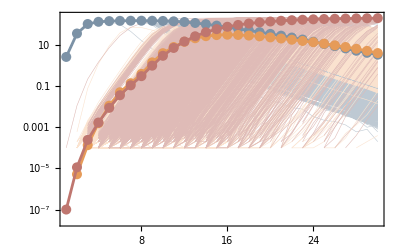

```mathematica
Show[
ListLogPlot[tab⟦1;;1000,1⟧,PlotStyle->Directive[Lighter[wwcol,0.5],Thickness[0.001]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003],16],FrameLabel->None],
ListLogPlot[tab⟦1;;1000,2⟧,PlotStyle->Directive[Lighter[rwcol,0.7],Thickness[0.001]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003],16],FrameLabel->None],
ListLogPlot[tab⟦1;;1000,3⟧,PlotStyle->Directive[Lighter[rrcol,0.5],Thickness[0.001]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003],16],FrameLabel->None],
ListLogPlot[tab⟦1001,1⟧,Mesh->True,MeshStyle->PointSize[0.018],PlotStyle->Directive[wwcol,Thickness[0.005]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003],16],FrameLabel->None],
ListLogPlot[tab⟦1001,2⟧,Mesh->True,MeshStyle->PointSize[0.018],PlotStyle->Directive[Darker[rwcol,0.05],Thickness[0.005]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003],16],FrameLabel->None],
ListLogPlot[tab⟦1001,3⟧,Mesh->True,MeshStyle->PointSize[0.018],PlotStyle->Directive[rrcol,Thickness[0.005]],Joined->True,Frame->True,FrameStyle->Directive[Black,Thickness[0.003],16],FrameLabel->None],
PlotRange->{Automatic,{-17.5,5.5}},Axes->None]
```

## Pie charts

```mathematica
onlydata⟦1,{9,12,13,14,15}⟧
```

{RRSSplants,RRRSplants,SSRRplants,RSRRplants,RRRRplants}

```mathematica
piedata=Table[onlydata=data⟦j⟧⟦1;;-31⟧;
onlyseason30=onlydata⟦-1000;;⟧;
sum=(*onlyseason30⟦All,9⟧+onlyseason30⟦All,12⟧+*)onlyseason30⟦All,13⟧+onlyseason30⟦All,14⟧+onlyseason30⟦All,15⟧;
(Length[sum]-Sort[Tally[sum]]⟦1,2⟧)/10//N,{j,1,Length[data],1}]
```

{99.6}

```mathematica
PieChart[{piedata⟦1⟧,100-piedata⟦1⟧},ChartStyle->{Directive[ Gray,Opacity[0.75]],White},
ChartLabels->Placed[{Style[ToString[piedata⟦1⟧]<>"% contain\n resistant plants",24,Black]},"RadialCallout"],ImageSize->Medium,ImagePadding->{{None,150},{-10,-10}}]
```

-Graphics-